```mathematica
SetDirectory[NotebookDirectory[]];
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
<<MaTeX`;
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools}"}];
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
plotsDir = "../../plots/plots-102-hist";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
data[1] = Import["../../runs/Trials/N7K9/74988019.dat"];
(*data[2] = Import["../../runs/Trials/N8K9/85145990.dat"];
data[3] = Import["../../runs/Trials/N8K9/93249996.dat"];*)
```

```mathematica
Evaluate[Array[rad, 1]] = (radius/@data[#]&)/@Range[1];
```

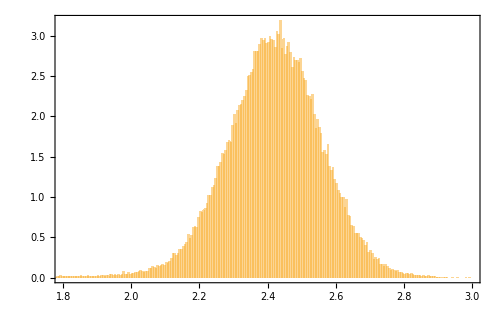

```mathematica
plt1 = Histogram[{rad[1][[All, 2]](*, rad[2][[All,2]], rad[3][[All,2]]*)}, 500,"PDF",
ChartLegends->MaTeX[{"a", "b", "c"}, "DisplayStyle"->False],
Frame->True,
FrameStyle->Black,
FrameLabel->MaTeX[{"\\Tr X^2", "\\rho"}],
BaseStyle->texStyle,(*
FrameTicks->{{With[{ticks = Range[0.0, 3.5, 0.5]}, Thread[{ticks, MaTeX[ticks, "DisplayStyle"->False]}]], None}, {With[{ticks = Range[1.8, 3.0, 0.2]}, Thread[{ticks, MaTeX[ticks, "DisplayStyle"->False]}]], None}},*)
Axes->False,
PlotRange->{{1.8, 3.0}, Automatic},
ImageSize->500
];
(*Export[plotsDir<>"/histogram-T-10000.pdf", plt1];*)
plt1
```

```mathematica
FindDistribution[rad[1][[All, 2]]]
```

LogisticDistribution[2.42017,0.0796193]

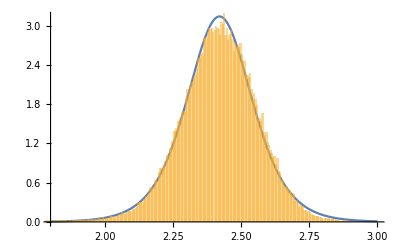

```mathematica
Show[Plot[PDF[LogisticDistribution[2.420171628267401,0.07961933226399837]][x], {x, 1.8, 3.0}], plt1]
```

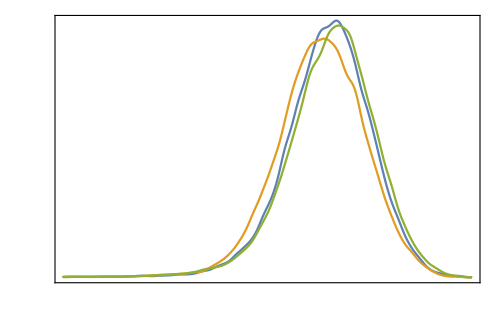

```mathematica
plt2 = SmoothHistogram[{rad[1][[All, 2]], rad[2][[All,2]], rad[3][[All,2]]},
PlotLegends->MaTeX[{"a", "b", "c"}, "DisplayStyle"->False],
Frame->True,
FrameStyle->Black,
FrameLabel->MaTeX[{"\\Tr X^2", "\\rho"}],
BaseStyle->texStyle,
FrameTicks->{{With[{ticks = Range[0.0, 3.5, 0.5]}, Thread[{ticks, MaTeX[ticks, "DisplayStyle"->False]}]], None}, {With[{ticks = Range[1.8, 3.0, 0.2]}, Thread[{ticks, MaTeX[ticks, "DisplayStyle"->False]}]], None}},
Axes->False,
PlotRange->{{1.8, 3.0}, Automatic},
ImageSize->500
];
Export[plotsDir<>"/smooth-histogram-T-10000.pdf", plt2];
plt2
```